# Chapter 7 Robust Fitting

In this chapter we discuss ways to circumvent a problem that was discussed in Chapter 4: least-squares techniques are not resistant to a wild data point. Such wild data points are often called “outliers.” The “robust” fitters discussed here avoid that weakness of least-squares techniques. One price that is paid, however, is that explicit errors in the data are ignored, and no truly meaningful estimates of errors in the fitted parameters are possible.  Also, these techniques are slower than conventional methods.

There is also a serious danger in these techniques. They assume that the model, either a line or a curve, is correct for the data and any data points that are not consistent with the model are suppressed. Very few scientific advances would occur if researchers always suppressed data that does not match preconceived expectations. The topic of suppressing or rejecting measurements is also discussed in Section 3.2.4.

The discussion below assumes some familiarity with the concepts and syntax discussed in Chapter 4. The LinearFit function introduced in that chapter should usually be tried before using the techniques discussed here.

## 7.1 Introduction

### 7.1.1 Using the Median

As has been mentioned many times, the mean or average is not resistant to a wild data point, which will badly distort the result of the calculation. It is in exactly this sense that least-squares techniques in general are not resistant.

We have also mentioned numerous times that the median is resistant to a wild datum — that is, it is “robust” — and that fact is used in the RobustLineFit function introduced in this subsection. The central idea is that the routine divides the data into three groups based on the value of the independent variable. Then the medians of the independent and dependent variables are calculated for each group, and a straight-line fit is made to these medians.

We first load and display some data on radioactive dating.

```mathematica
Needs["EDA`"]
```

```mathematica
LoadData[CThDating]
```

LoadData::name: Loading: CThDatingData

```mathematica
?CThDatingData
```

CThDatingData compares the dating of samples of coral using two
	different techniques: carbon-14 and thorium.  It can be viewed
	as a calibration of carbon-14 dating.  The data is from Edouard Bard,
	Bruno Hamelin, Richard G. Fairbanks, and Alan Zindler, Nature 345,
	(May, 1990), pg 405. The format of the data is {C14 age,
	{thorium age minus C14 age, error in thorium age minus C14 age}}, where
	all numbers are in years before the present. The errors are one standard
	deviation, not the two standard deviation errors given in the original
	source.

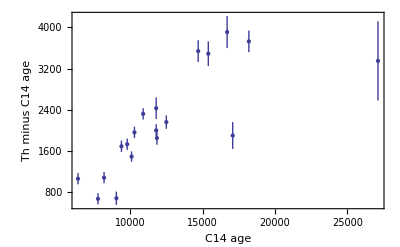

```mathematica
EDAListPlot[CThDatingData,Axes->False,Frame->True,PlotRange -> All, FrameLabel->{"C14 age","Th minus C14 age"}]
```

Further information on this data appears in Chapter 8.

If the thorium and carbon-14 dating agreed, the dependent variable should be zero within errors, which is clearly not the case. We fit the data to a straight line using the EDA function LinearFit.

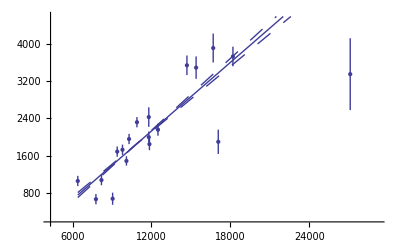

{a[0]→{-810.,130.},a[1]→{0.245,0.012},ChiSquared→156.953,DegreesOfFreedom→17}

```mathematica
LinearFit[CThDatingData,{0,1},a]
```

In this fit the two “outliers” in the data are having a marked effect on the results of the fit, as can be seen in the plots.

We do a robust straight-line fit to the data using RobustLineFit.

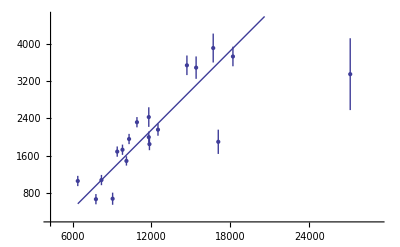

{a[0]→-1237.55,a[1]→0.282628,ChiSquared→167.932}

```mathematica
RobustLineFit[CThDatingData,a]
```

Note that the function requires a parameter name in its input, just like LinearFit, and by default returns rules for array members of that parameter, again just like LinearFit.

As discussed in Section 7.2, for this technique the concept of degrees of freedom has no meaning. Nonetheless, the function does return a ChiSquared using the errors in the experimental data as the weights. As we shall see, if the data has no explicit errors, a SumOfSquares is returned. In both cases, interpreting this number is indirect.

We examine the data.

```mathematica
CThDatingData
```

{{6400,{1060.,110.}},{7780,{670.,110.}},{8200,{1080.,110.}},{9050,{680.,130.}},{9400,{1690.,110.}},{10100,{1490.,100.}},{9800,{1730.,110.}},{10300,{1960.,110.}},{10900,{2320.,110.}},{11850,{1850.,130.}},{11800,{2000.,120.}},{11800,{2430.,210.}},{12500,{2160.,130.}},{14700,{3540.,210.}},{15400,{3490.,240.}},{17085,{1900.,260.}},{16700,{3910.,310.}},{18200,{3729.,210.}},{27120,{3350.,770.}}}

This shows that the two “wild” data points are at the end and the fourth from the end. We form a new data set with these two points dropped.

```mathematica
dropData=Drop[Drop[CThDatingData,-1],-3];
```

Fitting this to a straight line yields almost the same fit that we got for the full data set with RobustLineFit.

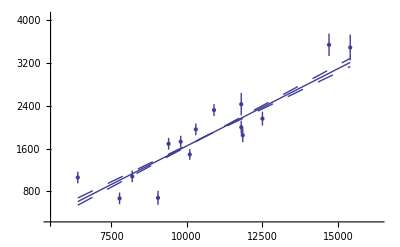

{a[0]→{-1240.,170.},a[1]→{0.289,0.016},ChiSquared→102.542,DegreesOfFreedom→13}

```mathematica
LinearFit[dropData,{0,1},a]
```

The advantage of RobustLineFit, however, is that in some sense it provides an “objective” estimate of whether or not a data point is wild, and does not involve explicitly throwing out any data.

As a final example using RobustLineFit, we return to the ganglion data already discussed in Chapters 4 and 6.

```mathematica
LoadData[Ganglion]
```

LoadData::name: Loading: GanglionData

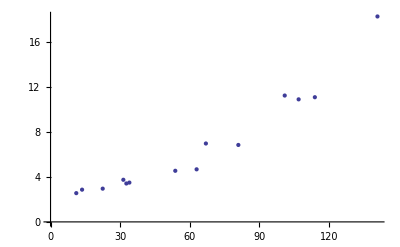

```mathematica
EDAListPlot[GanglionData]
```

So far, we have (1) fit the data to a parabola as well as a line, (2) fit the data to a straight line with the last data point dropped, and (3) done a loess fit to the residuals of various linear fits. We now do a robust fit to a line.

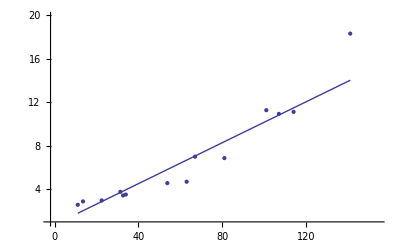

{a[0]→0.736124,a[1]→0.0940828,SumOfSquares→29.0146}

```mathematica
RobustLineFit[GanglionData,a]
```

Here again, the result gives us some indication that a straight line is not a good model for this data unless we treat the last data point as an outlier.

### 7.1.2 Using Weighting Techniques

Another way to do robust fitting is to realize that the data points we wish to suppress are those with high residuals. Say we have done a fit and the residuals for each data point are the following.

```mathematica
res = {res1, res2, ... , resN}
```

We form a set of weights.

```mathematica
weights = {w1, w2, ..., wN}
```

First we define a cutoff.

```mathematica
cutoff = 6 * Median[ Abs[res] ]
```

Values of the dependent value greater than this cutoff are set to zero. For values smaller than the cutoff, the weights are “bi-square” weights of the residuals. For example, if the cutoff is 15 the weights look like this.

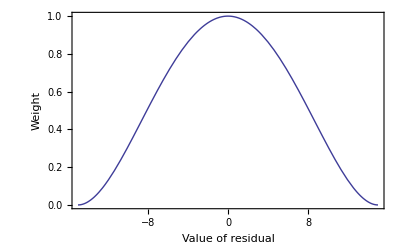

```mathematica
cutoff=15;
bisquare[x_]:=(1-x^2)^2
Plot[bisquare[res/cutoff],{res,-cutoff,cutoff},Axes->False,Frame->True,FrameLabel->{"Value of residual","Weight"}]
```

A brief technical note: Because we are going to convert these weights to errors below by taking the reciprocal of them, the minimum value of a weight cannot be exactly zero. Instead these weights are set to the minimum positive number that can be used on a particular computer, $MinMachineNumber.

The weights are converted to effective errors in the dependent variable.

```mathematica
erry=√(1/weights)
```

Then the fit is iterated until it converges.

This is exactly the technique used by RobustCurveFit.

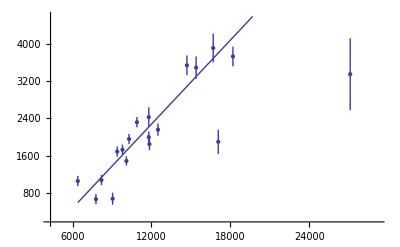

{a[0]→-1323.43,a[1]→0.300054,PseudoChiSquared→1.29636×10^6,DegreesOfFreedom→15}

```mathematica
RobustCurveFit[CThDatingData,{0,1},a]
```

Note that the input arguments to RobustCurveFit are identical to those of the EDA function LinearFit. LinearFit is actually used internally by RobustCurveFit.

The PseudoChiSquared returned by the routine is the chi-squared statistic calculated assuming that the errors in the dependent variable generated by the bi-square weights are the correct errors. Thus, its interpretation is indirect.

The DegreesOfFreedom returned is the number of data points minus the number of parameters to which we are fitting (the standard definition) minus the number of data points whose weights are set to zero.

If the model matches the data reasonably well, then RobustCurveFit should produce a fit with little or no difference from LinearFit. Using the ganglion data once more illustrates this.

```mathematica
LinearFit[GanglionData,{0,2},a,ShowFit->False]
```

{a[0]→{2.56,0.25},a[2]→{0.000757,0.000032},PseudoErrorY→0.692244,SumOfSquares→5.75043,DegreesOfFreedom→12}

```mathematica
RobustCurveFit[GanglionData,{0,2},a,ShowFit->False]
```

{a[0]→2.54529,a[2]→0.000764631,PseudoChiSquared→2.85032,DegreesOfFreedom→12}

Note that we could not have used RobustLineFit for this, since it is only capable of fitting to straight lines.

Finally, RobustCurveFit can be used as a robust averager of data. For example, the following command generates 20 data points fairly close to 1.5 and a single data point equal to 100.

```mathematica
SeedRandom[1234];
mydata=Table[1.5+RandomReal[{-0.1,0.1}],{20}];
mydata=Insert[mydata,100,5];
```

We use the Mean and Median functions that are Mathematica built-in commands..

```mathematica
Mean[mydata]
```

6.20135

```mathematica
Median[mydata]
```

1.50875

Fitting this data to a polynomial with powers of {0} means we have forced the slope and all other terms involving the independent variable to zero. Thus, a[0] should be the mean.

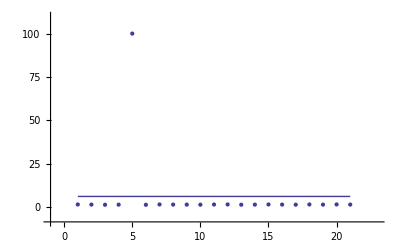

{a[0]→6.20135,PseudoErrorY→21.4921,SumOfSquares→9238.17,DegreesOfFreedom→20}

```mathematica
LinearFit[mydata,{0},a,ReturnErrors->False]
```

This result shows clearly that the least-square technique used by LinearFit is not robust and the answer is exactly the same as produced above by Mean. However, using RobustCurveFit gives a robust answer.

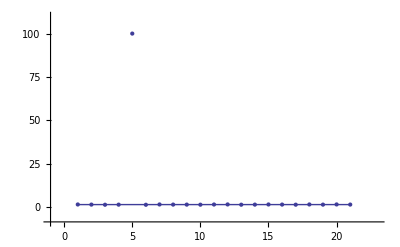

{a[0]→1.51164,PseudoChiSquared→0.0585327,DegreesOfFreedom→19}

```mathematica
RobustCurveFit[mydata,{0},a]
```

In fact, this result is almost exactly the average of all the numbers except the one outlier.

```mathematica
Mean[Drop[mydata,{5}]]
```

1.51142

The result of RobustCurveFit is also within 0.3% of the median of the full data set.

## 7.2 Details

```mathematica
Needs["EDA`"]
```

### 7.2.1 RobustCurveFit

The algorithm used by RobustCurveFit is described in Section 7.1.2. The function has the following options.

```mathematica
TableForm[Options[RobustCurveFit]]
```

MaximumIterations→5
ReturnErrors→False
ReturnFunction→False
ShowFit→True
EDAShowProgress→False
UseSignificantFigures→False

The LinearFit function discussed in Chapter 4 has these same options with the same meanings.

Experience has shown that a MaximumIterations of 5 should almost always be sufficient for RobustCurveFit, but the option allows the number to be increased if necessary.

The ReturnErrors option, if set to True, causes the routine to attempt to estimate and return errors in the fitted parameters.

```mathematica
RobustCurveFit[CThDatingData,{0,1},a,ReturnErrors->True,ShowFit->False]
```

{a[0]→{-1323.43,0.974429},a[1]→{0.300054,0.0000818571},PseudoChiSquared→1.29636×10^6,DegreesOfFreedom→15}

However, these numbers should be taken with a “grain of salt” since the errors in the dependent variable are fakes: they are generated from the bi-square weighted residuals.

Nonetheless, to have these errors in the fit parameters adjust the significant figures in the answer, the UseSignificantFigures option may be used.

```mathematica
RobustCurveFit[CThDatingData,{0,1},a,ReturnErrors->True,UseSignificantFigures->True,ShowFit->False]
```

{a[0]→{-1323.4,1.},a[1]→{0.300054,0.000082},PseudoChiSquared→1.29636×10^6,DegreesOfFreedom→15}

To have RobustCurveFit return a function of an independent variable, say c14, instead of a list of rules, the ReturnFunction option may be used.

```mathematica
RobustCurveFit[CThDatingData,{0,1},c14,ReturnFunction->True,ShowFit->False]
```

{-1323.43+0.300054 c14}

The EDAShowProgress option enables monitoring of the progress of the function.

```mathematica
result=RobustCurveFit[CThDatingData,{0,1},a,EDAShowProgress->True,ShowFit->False]
```

19 data points, each with 3 variables.

Note: the data is sorted by independent

variable.

19 data points, each with 3 variables.

Iteration 1 using singular value decomposition.

Chi-squared = 2.06698×10^6

Parameter values: {-1174.72,0.284187}

Iteration: 1 ChiSquared = 2.06698×10^6

Suppressed data points at: {{19}}

{a[0],a[1]} = {-1174.72,0.284187}

19 data points, each with 3 variables.

Iteration 1 using singular value decomposition.

Chi-squared = 1.6025×10^6

Parameter values: {-1306.27,0.298082}

Iteration: 2 ChiSquared = 1.6025×10^6

Suppressed data points at: {{17},{19}}

{a[0],a[1]} = {-1306.27,0.298082}

19 data points, each with 3 variables.

Iteration 1 using singular value decomposition.

Chi-squared = 1.54442×10^6

Parameter values: {-1323.43,0.300054}

Iteration: 3 ChiSquared = 1.54442×10^6

Suppressed data points at: {{17},{19}}

{a[0],a[1]} = {-1323.43,0.300054}

{a[0]→-1323.43,a[1]→0.300054,PseudoChiSquared→1.29636×10^6,DegreesOfFreedom→15}

Finally, as already seen in the examples above, setting ShowFit to False suppresses the graph of the results. This last example has stored the fit parameters in result. The graph can be generated at a later time with the EDA function ShowLinearFit, which is discussed in Section 4.5.2.

```mathematica
ShowLinearFit[CThDatingData,{0,1},a,result]
```

-Graphics-

An extensive discussion of the bi-square weighting method used by RobustCurveFit can be found in Cleveland.

Reference: William S. Cleveland, Visualizing Data (AT&T Bell Laboratories, 1993), passim.

### 7.2.2 RobustLineFit

As mentioned in Section 7.1.1, the central ideal of RobustLineFit is that it divides the data into three groups based on the value of the independent variable. We will call these groups Left, Middle, and Right, respectively. Then the medians of the independent and dependent variables are calculated for each of the three groups, and a straight line is fit to the medians.

The three-group median method implemented by RobustLineFit is derived from Tukey, although in its original form the algorithm is not always stable. Thus, here we use a modification with greatly improved stability due to Johnstone and Velleman.

References:

John W. Tukey, Exploratory Data Analysis (John Wiley, 1970).

I. Johnstone and P.F.Velleman, 1981 Proc. Statistical Computation Section, American Statistics Assoc. (1982), p. 218.

RobustLineFit has the following options.

```mathematica
TableForm[Options[RobustLineFit]]
```

Groups→Automatic
MaximumIterations→5
ReturnFunction→False
ShowFit→True
EDAShowProgress→False

All of these options except Groups have identical meanings to the same options for LinearFit and RobustCurveFit. We will discuss Groups in a moment.

Experience has shown that a MaximumIterations of 5 is almost always sufficient, although the option allows it to be increased if necessary.

When ReturnFunction is set to True, the routine returns a function of the independent variable parameter, instead of a set of rules for a parameter.

Setting ShowFit to False suppresses the display of the results of the fit. The EDA function ShowLinearFit can later display the result from RobustLineFit.

As usual, EDAShowProgress gives information about the progress of the fit. Below are some examples using this option.

The Groups option controls how the data are divided into three groups. When it is set to Automatic, the groups are as close as possible to having the same number of data points in them. However, no two groups are allowed to have the same value of the independent variable in them, so some shifting is necessary. The following example illustrates this shifting.

```mathematica
SeedRandom[1234];
mydata=Sort[Table[i=RandomInteger[{1,5}];{i,i+RandomReal[{-i/10,i/10}]},{i,10}]]
```

{{1,0.920589},{1,1.0073},{1,1.04238},{2,1.86846},{2,2.03113},{3,3.22797},{4,3.79656},{4,4.09079},{5,4.65821},{5,4.93949}}

```mathematica
RobustLineFit[mydata,a,ShowFit->False,EDAShowProgress->True]
```

Initial groups sizes: {3,4,3}

Final group sizes are: {3,3,4}

First slope estimate: 0.962057

Second slope estimate: 0.960207

{a[0]→0.0646323,a[1]→0.960207,SumOfSquares→0.201826}

Although it tries to be smart about forming groups, occasionally RobustLineFit fails.

```mathematica
SeedRandom[2345];
mydata=Sort[Table[i=RandomInteger[{1,5}];{i,i+RandomReal[{-i/10,i/10}]},{i,10}]]
```

{{1,1.02983},{2,1.80915},{3,2.83009},{4,3.92608},{4,4.02524},{4,4.09478},{4,4.28901},{4,4.34583},{5,4.78329},{5,5.32948}}

```mathematica
RobustLineFit[mydata,a,ShowFit->False,EDAShowProgress->True]
```

Initial groups sizes: {3,4,3}

RobustLineFit::unbalanced: Warning: the partitions are of size {3, 5, 2}, which is very unbalanced.

Final group sizes are: {3,5,2}

First slope estimate: 1.08241

Second slope estimate: 1.08241

{a[0]→-0.269644,a[1]→1.08241,SumOfSquares→0.394734}

We can force the program to use group sizes of 2, 2, and 6, respectively.

```mathematica
RobustLineFit[mydata,a,ShowFit->False,EDAShowProgress->True,Groups->{2,2,6}]
```

Initial groups sizes: {2,2,6}

RobustLineFit::unbalanced: Warning: the partitions are of size {2, 1, 7}, which is very unbalanced.

Final group sizes are: {2,1,7}

First slope estimate: 1.14781

Second slope estimate: 1.07012

{a[0]→-0.220461,a[1]→1.07012,SumOfSquares→0.384767}

Just specifying ratios of the group sizes has the same effect.

```mathematica
RobustLineFit[mydata,a,ShowFit->False,EDAShowProgress->True,Groups->{1,1,3}]
```

Initial groups sizes: {2,2,6}

RobustLineFit::unbalanced: Warning: the partitions are of size {2, 1, 7}, which is very unbalanced.

Final group sizes are: {2,1,7}

First slope estimate: 1.14781

Second slope estimate: 1.07012

{a[0]→-0.220461,a[1]→1.07012,SumOfSquares→0.384767}

Note the warning message generated above. As discussed below, there is a desire for groups of about the same size.

The Left and Right groups alone are used to determine the slope of the line. Thus, there is a balance needed between having a reasonable sized group and having these two groups fairly far away from each other. Once the slope has been determined through iteration, the intercept is calculated from the residuals and the median of the independent variable of the Middle group.

There is a history of two-group and three-group median methods going back to at least 1940. A review of that history and further details of the algorithm used by RobustLineFit can be found in Emerson and Hoaglin.

Reference:  John D. Emerson and David C. Hoaglin, in David C. Hoaglin, Frederick Mosteller, and John W. Tukey, eds., Understanding Robust and Exploratory Data Analysis (Wiley-Interscience, 1983), Chapter 5.

### 7.2.3 Comparing RobustCurveFit and RobustLineFit

When doing a robust fit to a line, RobustLineFit is much faster than RobustCurveFit. For example, below we generate some made-up data of 1000 points of which 5 are outliers.

```mathematica
SeedRandom[1234];
mydata=Table[If[Mod[i,200]==0,{i,i+2000+RandomReal[{-i/10,i/10}]},{i,i+RandomReal[{-i/10,i/10}]}],{i,10000}];
```

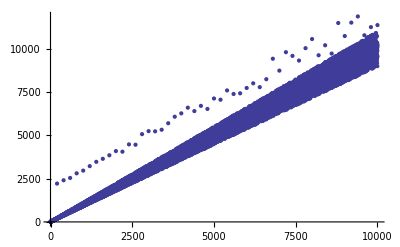

```mathematica
EDAListPlot[mydata,PlotJoined->True,PlotRange->All]
```

We fit to a straight line and generate timing information.

```mathematica
Timing[RobustLineFit[mydata,a,ShowFit->False]]
```

{0.031,{a[0]→-2.63467,a[1]→1.00397,SumOfSquares→1.2832×10^9}}

```mathematica
Timing[RobustCurveFit[mydata,{0,1},a,ShowFit->False]]
```

{0.437,{a[0]→-8.30378,a[1]→1.00353,PseudoChiSquared→3.79225×10^8,DegreesOfFreedom→9948}}

Although you probably will not get exactly the same timing numbers on your computer, you will find that RobustLineFit is much faster than RobustCurveFit for most large datasets. Considering the details described above of how the two routines work, this result is hardly surprising.

Of course, the comparative slowness of RobustCurveFit is balanced by the fact that it can fit to arbitrary polynomials.

In addition, RobustLineFit devotes most of its effort to the determination of the slope, which is usually the parameter of most interest. RobustCurveFit, on the other hand, emphasizes the slope and intercept essentially equally when fitting to a line.

## 7.3 Summary of the RobustFit Package

```mathematica
Needs["EDA`"]
```

```mathematica
Information["RobustCurveFit",LongForm->False]
```

RobustCurveFit[data, powers, parameter] does a bi-squared residual
	weighted fit of data to a polynomial specified by powers. By
	default, it returns the result as a list of rules for parameter.

```mathematica
TableForm[Options[RobustCurveFit]]
```

MaximumIterations→5
ReturnErrors→False
ReturnFunction→False
ShowFit→True
EDAShowProgress→False
UseSignificantFigures→False

```mathematica
Information["MaximumIterations",LongForm->False]
```

MaximumIterations is an option for various routines that use	iterative techniques. It specifies the maximum number
	of iterations to perform before quitting.

```mathematica
Information["ReturnErrors",LongForm->False]
```

ReturnErrors is an option for various fitting routines. If set to	True, then the routine returns errors in the fitted parameters.	Otherwise, it does not.

```mathematica
Information["ReturnFunction",LongForm->False]
```

ReturnFunction is an option for various fitting routines. If
	set to False, then the fit will be returned as a set of rules	involving the "parameter" given in the call to the routine.
	If set to True, then the fit will be returned as a function
	and the independent variable is taken to be "parameter".

```mathematica
Information["ShowFit",LongForm->False]
```

ShowFit is an option for various fitting routines. If set to True,
	then a graphical display of the results of the fit is displayed.

```mathematica
Information["EDAShowProgress",LongForm->False]
```

EDAShowProgress is an option for various routines. When set to True, the
	routine will print messages showing its progress in performing
	its tasks. If set to False, no such information is printed.

```mathematica
Information["UseSignificantFigures",LongForm->False]
```

UseSignificantFigures is an option for various routines. When set to
	True, the routine will use AdjustSignificantFigures on numbers with
	associated errors, so that the error determines the number of
	significant figures in the number itself. If set to False, no
	such adjustment is performed.

```mathematica
Information["RobustLineFit",LongForm->False]
```

RobustLineFit[data, parameter] fits data to a straight-line using a
	stable three-group median resistant method, and by default, returns
	the result as a list of rules for parameter.

```mathematica
TableForm[Options[RobustLineFit]]
```

Groups→Automatic
MaximumIterations→5
ReturnFunction→False
ShowFit→True
EDAShowProgress→False

```mathematica
Information["Groups",LongForm->False]
```

Groups is an option for RobustLineFit. By default, the three group
	sizes are set as close as possible to a ratio of 1:1:1. However, the
	requirement that repeated values of the independent variable are all
	in the same partition or in a small data set may alter that ratio somewhat.
	If Groups is set to {num1, num2, num3}, n is the number of data
	points, and Mod[n, num1 + num2 + num3] = 0, those ratios are used instead.

```mathematica
Information["MaximumIterations",LongForm->False]
```

MaximumIterations is an option for various routines that use	iterative techniques. It specifies the maximum number
	of iterations to perform before quitting.

```mathematica
Information["ReturnFunction",LongForm->False]
```

ReturnFunction is an option for various fitting routines. If
	set to False, then the fit will be returned as a set of rules	involving the "parameter" given in the call to the routine.
	If set to True, then the fit will be returned as a function
	and the independent variable is taken to be "parameter".

```mathematica
Information["ShowFit",LongForm->False]
```

ShowFit is an option for various fitting routines. If set to True,
	then a graphical display of the results of the fit is displayed.

```mathematica
Information["EDAShowProgress",LongForm->False]
```

EDAShowProgress is an option for various routines. When set to True, the
	routine will print messages showing its progress in performing
	its tasks. If set to False, no such information is printed.